1. NALOGA

```mathematica
v0={10,3};
GG=9.81;
H=10;
a={0,-GG};
X0={0,H};
v[t_]:={v0[[1]],v0[[2]]-GG*t}
v[t_]:=v0+a*t
X[t_]:=X0+v0*t+a*t^2/2
```

```mathematica
v[t]
```

{10,3-9.81 t}

```mathematica
X[t]
```

{10 t,10+3 t-4.905 t^2}

```mathematica
v0+a*t
```

{10,3-9.81 t}

```mathematica
X0+v0+t+a*t^2/2
```

{10+t,13+t-4.905 t^2}

```mathematica
SlikaTocke[t_] := {PointSize[0.03],Point[X[t]]};
Graphics[SlikaTocke[1]]
```

-Graphics-

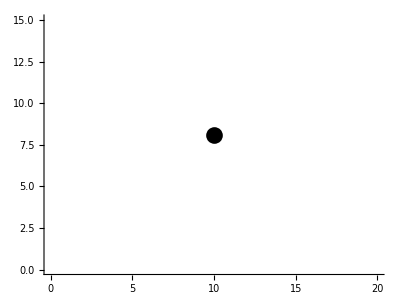

```mathematica
Graphics[SlikaTocke[1], Axes->True, PlotRange-> {{0,20}, {0, 15}}]
```

```mathematica
SlikaTocke[t_]:={PointSize[0.03],Point[X[t]]};
Manipulate[Graphics[{SlikaTocke[t],Arrow[{{1,1},{2,2}}]}, Axes->True,PlotRange->{{0,20},{0,15}}],{t,0,3}]
```

```mathematica
SlikaVektorja[t_] := {Arrowheads[0.05], Arrow[{X[t], X[t]+v[t]}]}
Manipulate[Graphics[{SlikaTocke[t] ,SlikaVektorja[t]},Axes->True, PlotRange->{{0,20},{0,15}}, AspectRatio->Automatic],{t,0,1.076}]
```

```mathematica
Hitrost = √(v0[[1]]^2+v0[[2]]^2)
sinkot =v0[[2]]/ Hitrost //N
NajvišjaTočka = (Hitrost^2* sinkot^2)/(2*GG)+ H
casLetaDoNajvišjeTočke = (2*Hitrost*sinkot)/(GG * 2)
domet  =Hitrost^2 *Sin[2*ArcSin[sinkot]]/GG + H
casLeta= casLetaDoNajvišjeTočke  + (2*NajvišjaTočka/GG) ^(1/2)
absHitrosti=√((v[casLeta][[1]])^2  + (v[casLeta][[2]])^2)
```

√109

0.287348

10.4587

0.30581

16.1162

1.76604

17.47

2. NALOGA

```mathematica
r111=Ravnina[{-1,-1,-1},{1,1,1}]
Slika[Ravnina[n_,v_]]:=Hyperplane[n,v]
Format[r_Ravnina]:=Graphics3D[Slika[r]]
Normala[Ravnina[n_,v_]]:=n
Normala[r111]
```

Ravnina[{-1,-1,-1},{1,1,1}]

{-1,-1,-1}

```mathematica
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
ravnine = {rx, ry, rz, r111}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SlikaNormale[Ravnina[n_,v_]]:=Arrow[{v,v+n}]
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

```mathematica
ravnine = {r111, rx};
obeSliki[r_Ravnina] := {Slika[r],SlikaNormale[r]}
Graphics3D[Map[obeSliki, ravnine]]
```

-Graphics3D-

```mathematica
SlikaNormale[Ravnina[n_,v_]]:=Arrow[{v,v+n}]
ravnine = {rx, ry, rz, r111};
slikeRavnin = Map[Slika, ravnine];
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

```mathematica
EnacbaRavnine[Ravnina[n_,r_]]:=Module[{x, y,z,levi,desni},
levi =(n[[1]])*x + (n[[2]])*y + (n[[3]])*z;
desni = n[[1]]*r[[1]]+ n[[2]]*r[[2]] + n[[3]]*r[[3]];
Return levi = desni];
EnacbaRavnine[r111]
```

-3

3. NALOGA

```mathematica
AA ={0,0,0};
BB ={1,0,0};
CC ={1,1,0};
DD = {0,1,1};
Prizma[AA_,BB_,CC_,DD_]={AA,BB,CC,DD}
Graphics3D[Parallelepiped[{0,0,0},{{1,0,0},{1,1,0},{0,1,1}}]]
```

{{0,0,0},{1,0,0},{1,1,0},{0,1,1}}

-Graphics3D-